## Testing on stochastic decay with production

```mathematica
fCalculateA0[A_,t_,k1_,k2_]:=Block[{a0=A k1 + k2,r1=RandomReal[],r2=RandomReal[],τ},τ=(1/a0)Log[1/r1];If[r2<k2/a0,{t+τ,A+1},{t+τ,A-1}]]
fGillespie[A0_,k1_,k2_,tmax_]:=NestWhileList[fCalculateA0[#[[2]],#[[1]],k1,k2]&,{0,A0},#[[1]]<tmax&]
fInterpolationCorrect[f_,tobs_]:=f[tobs]+1
fGillespie10[A0_,k1_,k2_]:=Block[{samples=fGillespie[A0,k1,k2,10],f},f=Interpolation[samples,InterpolationOrder->1];If[f[10]>0,f[10],0.000001]]
```

```mathematica
test=fGillespie[0,0.1,1,100];
```

```mathematica
f=Interpolation[test,InterpolationOrder->1];
```

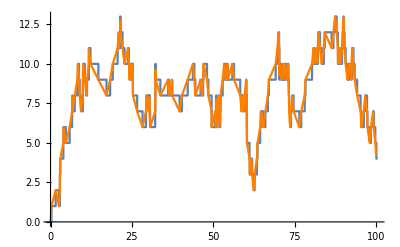

```mathematica
Show[ListStepPlot[test],Plot[f[t],{t,0,100},PlotStyle->Orange]]
```

### Generating a target by forward simulation

```mathematica
test=Table[fGillespie10[0,0.15+0.1 RandomReal[],1],{10000}];
```

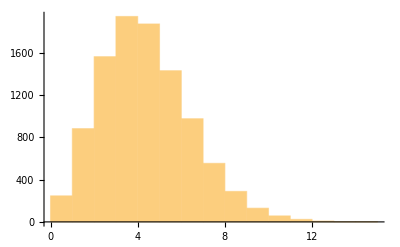

```mathematica
Histogram[test]
```

### Estimate contour volumes as per Troy’s first step

```mathematica
target=SmoothKernelDistribution[test];
n=100000;
k1=RandomVariate[UniformDistribution[{0,1}],n];
q1=ParallelTable[fGillespie10[0,k1[[i]],1],{i,1,Length@k1,1}];
```

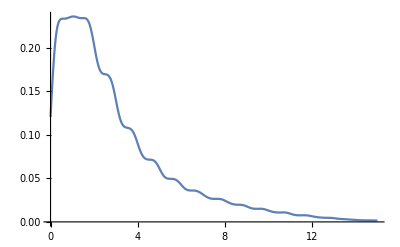

```mathematica
dens1=SmoothKernelDistribution[q1];
Plot[PDF[dens1,x],{x,0,15}]
```

### Calculate value of pdf for target and prior for each sampled q value

```mathematica
data1=ParallelTable[PDF[target,q1[[i]]],{i,1,Length@q1,1}];
pfprior1=ParallelTable[PDF[dens1,q1[[i]]],{i,1,Length@q1,1}];
ratio=data1/pfprior1;
lnormrat=ratio/Max[ratio];
muKept=Table[If[lnormrat[[i]]>RandomReal[],{q1[[i]],k1[[i]]},-1],{i,1,Length@lnormrat}];
muFinal=DeleteCases[muKept,-1];
```

### Compare a histogram of the accepted q values with the target

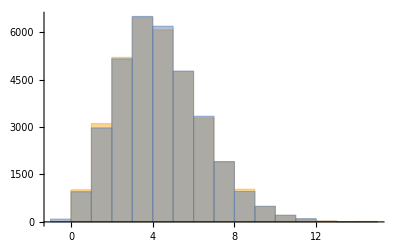

```mathematica
Histogram[{muFinal[[All,1]],RandomVariate[target,{Length@muFinal}]}]
```

### Examine accepted values of k1

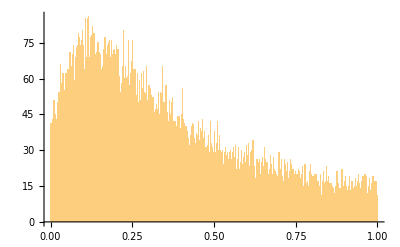

```mathematica
Histogram[muFinal[[All,2]],1000]
```

### Use accepted samples of k1 as input to SSA and compare q samples with target -- they are different

```mathematica
qTest=ParallelTable[fGillespie10[0,muFinal[[All,2]][[i]],1],{i,1,Length@muFinal[[All,2]],1}];
```

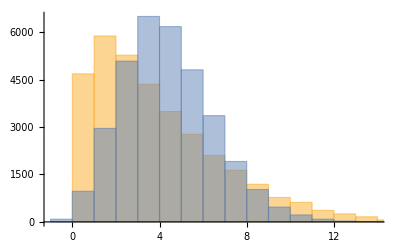

```mathematica
Histogram[{qTest,RandomVariate[target,{Length@qTest}]}]
```